```mathematica
(*Import packages*)
<<PVReduce`
$LoadFeynArts=True;
$FeynCalcStartupMessages=False;
<<FeynCalc`
$FAVerbose=0;
```

Package-X v2.1.1 [patched 22/08/2020], by Hiren H. Patel
For more information, see the

PVReduce v0.1.0 [BETA] initialized.

Eps::shdw: Symbol Eps appears in multiple contexts {FeynCalc`,X`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

SpinorU::shdw: Symbol SpinorU appears in multiple contexts {FeynCalc`,X`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

SpinorV::shdw: Symbol SpinorV appears in multiple contexts {FeynCalc`,X`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

Contract::shdw: Symbol Contract appears in multiple contexts {FeynCalc`,X`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

DiracMatrix::shdw: Symbol DiracMatrix appears in multiple contexts {FeynCalc`,X`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
(*Why is this?*)
$KeepLogDivergentScalelessIntegrals=True;
```

```mathematica
(*Prettify four-momenta when printing*)
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[Subscript[p, i],TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(i\)]\)";
MakeBoxes[Subscript[p, j],TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(j\)]\)";
```

```mathematica
(*Set Mandelstam variables*)
FCClearScalarProducts[];
SetMandelstam[s, t, u, p1, p2, -Subscript[p, i], -Subscript[p, j], 0, 0, Subscript[m, i], Subscript[m, j]];
MandelstamParameters={s,t,u,Subscript[m, i]^2+Subscript[m, j]^2};
```

## Get Feynman diagrams

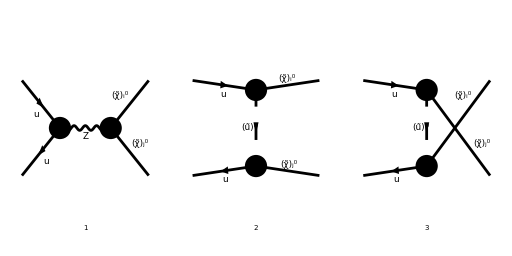

```mathematica
TreeDiagrams=InsertFields[CreateTopologies[0, 2->2], {F[3, {1}], -F[3, {1}]} -> {F[11, {i}], F[11, {j}]}, InsertionLevel -> {Classes}, Model -> MSSMQCD, Restrictions->{NoLightFHCoupling}];
Paint[TreeDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

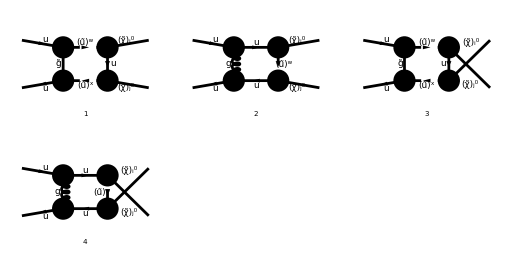

```mathematica
BoxDiagrams = InsertFields[CreateTopologies[1, 2->2,ExcludeTopologies->{Triangles,SelfEnergies,Tadpoles}], {F[3, {1}], -F[3, {1}]} -> {F[11, {i}], F[11, {j}]}, InsertionLevel -> {Classes}, Model -> MSSMQCD,Restrictions->{NoLightFHCoupling,NoElectronHCoupling},ExcludeParticles->{V[1],V[2],V[3],F[11],F[12],S[1],S[2],S[3],S[4]}];
Paint[BoxDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

## Convert diagrams to amplitudes

```mathematica
(*Replacement rules that are general for all amplitudes*)
(*Replacement rules for Z-boson couplings*)
(*Replacement rules for squark-quark-neutralino coupling*)
AmpSimplifyRules={
Index[Sfermion,5]:>A,
Index[Sfermion,6]:>M,
USf[args1__][a_,b_]:>Subscript[Q̃, a,b],
MNeu[a_]:>Subscript[m, a],
MSf[a_,b__]:>Subscript[m, Subscript[q̃, a]],
MGl:>Subscript[m, g̃],
Index[Neutralino,5]:>k,
SB:>Subscript[s, β],
CB:>Subscript[c, β],
TB:>Subscript[t, β],
SMP["e"]:>SMP["g_W"]SMP["sin_W"],
SMP["m_u"]->0,
SMP["sin_W"]:>Subscript[s, W],
SMP["cos_W"]:>Subscript[c, W]};
ZSimplifyRules={
4 Subscript[s, W]^2-3->-6 Subscript[C, L],
Subscript[s, W]^2->-3/2 Subscript[C, R],
ZNeu[i,4]:> (2 Subscript[O, ij]^L+ZNeu[i,3]Conjugate[ZNeu[j,3]])/Conjugate[ZNeu[j,4]],
Conjugate[Subscript[O, ij]^L]:>-Subscript[O, ij]^R};
QSimplifyRules={
ZNeu[a_,1] Subscript[Q̃, b_,2]:>-3/2Conjugate[Subscript[C, a,b]^R]Subscript[c, W]/Subscript[s, W],
Subscript[Q̃, b_,1] Conjugate[ZNeu[a_,2]]:>2 Subscript[C, a,b]^L-Subscript[Q̃, b,1] Subscript[s, W]/Subscript[c, W]Conjugate[ZNeu[a,1]]/3,
Conjugate[ZNeu[a_,1]]Conjugate[Subscript[Q̃, b_,2]]:>-3/2 Subscript[C, a,b]^R Subscript[c, W]/Subscript[s, W],
Conjugate[Subscript[Q̃, b_,1]](3ZNeu[a_,2] Subscript[c, W]+ZNeu[a_,1] Subscript[s, W]):>6Conjugate[Subscript[C, a,b]^L] Subscript[c, W]
};
```

```mathematica
(*Tree-level diagrams*)
{Subscript[M, s][0],Subscript[M, t][0],Subscript[M, u][0]} = FCFAConvert[CreateFeynAmp[TreeDiagrams],IncomingMomenta->{p1,p2}, OutgoingMomenta->{Subscript[p, i],Subscript[p, j]},ChangeDimension->D,UndoChiralSplittings->True,List->True,SMP->True,DropSumOver->True,LorentzIndexNames->{μ,ν},SUNIndexNames->{a,b}]//.AmpSimplifyRules
```

{-(g^μν Dot(φ(-p_2),(2 ⅈ g_W (s^W)^2 δ_Col1Col2 Dot(γ^μ,(γ̄)^6))/(3 c^W)+(ⅈ g_W (4 (s^W)^2-3) δ_Col1Col2 Dot(γ^μ,(γ̄)^7))/(6 c^W),φ(p_1)) Dot(φ(p^j,m^j),(ⅈ g_W Dot(γ^ν,(γ̄)^6) (ZNeu(i,3) Conjugate[ZNeu(j,3)]-ZNeu(i,4) Conjugate[ZNeu(j,4)]))/(2 c^W)+(ⅈ g_W Dot(γ^ν,(γ̄)^7) (ZNeu(j,4) Conjugate[ZNeu(i,4)]-ZNeu(j,3) Conjugate[ZNeu(i,3)]))/(2 c^W),φ(-p^i,m^i)))/((p^i+p^j)^2-m_Z^2),(Dot(φ(p^i,m^i),(2 ⅈ √2 (γ̄)^6 g_W s^W ZNeu(i,1) (Q̃)^(A,2))/(3 c^W)-(ⅈ (γ̄)^7 g_W (3 c^W m_W s^β (Q̃)^(A,1) Conjugate[ZNeu(i,2)]+m_W s^β s^W (Q̃)^(A,1) Conjugate[ZNeu(i,1)]))/(3 √2 c^W m_W s^β),φ(p_1)) Dot(φ(-p_2),(2 ⅈ √2 (γ̄)^7 g_W s^W δ_Col1Col2 Conjugate[ZNeu(j,1)] Conjugate[((Q̃)^(A,2))])/(3 c^W)-(ⅈ (γ̄)^6 g_W δ_Col1Col2 Conjugate[((Q̃)^(A,1))] (3 c^W ZNeu(j,2)+s^W ZNeu(j,1)))/(3 √2 c^W),φ(-p^j,m^j)))/((p^j-p_2)^2-m_((q̃)^A)^2),-(Dot(φ(p^j,m^j),(2 ⅈ √2 (γ̄)^6 g_W s^W ZNeu(j,1) (Q̃)^(A,2))/(3 c^W)-(ⅈ (γ̄)^7 g_W (3 c^W m_W s^β (Q̃)^(A,1) Conjugate[ZNeu(j,2)]+m_W s^β s^W (Q̃)^(A,1) Conjugate[ZNeu(j,1)]))/(3 √2 c^W m_W s^β),φ(p_1)) Dot(φ(-p_2),(2 ⅈ √2 (γ̄)^7 g_W s^W δ_Col1Col2 Conjugate[ZNeu(i,1)] Conjugate[((Q̃)^(A,2))])/(3 c^W)-(ⅈ (γ̄)^6 g_W δ_Col1Col2 Conjugate[((Q̃)^(A,1))] (3 c^W ZNeu(i,2)+s^W ZNeu(i,1)))/(3 √2 c^W),φ(-p^i,m^i)))/((p^i-p_2)^2-m_((q̃)^A)^2)}

```mathematica
(*Replace MSSMQCD Feynman rules with those from my thesis*)
(*This amounts to just redifinition of coupling parameters*)
Subscript[M, s][1]=Subscript[M, s][0]//.ZSimplifyRules//Simplify;
Subscript[M, t][1]=Subscript[M, t][0]//.QSimplifyRules//Simplify;
Subscript[M, u][1]=Subscript[M, u][0]//.QSimplifyRules//Simplify;
```

```mathematica
(*Box-loop diagrams*)
Subscript[M, box][0] = FCFAConvert[CreateFeynAmp[BoxDiagrams], IncomingMomenta->{p1,p2}, OutgoingMomenta->{Subscript[p, i],Subscript[p, j]},LoopMomenta->{qloop},ChangeDimension->D,UndoChiralSplittings->True,List->True,SMP->True,DropSumOver->True,LorentzIndexNames->{μ,ν},SUNIndexNames->{a,b,d,e,c}]//.AmpSimplifyRules
```

{-((ⅈ Dot(φ(-p_2),ⅈ √2 Conjugate[SqrtEGl] Conjugate[((Q̃)^(M,2))] (γ̄)^7 g_s T_Col2Col5^c-ⅈ √2 SqrtEGl Conjugate[((Q̃)^(M,1))] (γ̄)^6 g_s T_Col2Col5^c,γ·qloop+m_(g̃),ⅈ √2 SqrtEGl (γ̄)^6 (Q̃)^(A,2) g_s T_Col5Col1^c-ⅈ √2 Conjugate[SqrtEGl] (γ̄)^7 (Q̃)^(A,1) g_s T_Col5Col1^c,φ(p_1)) Dot(φ(p^j,m^j),(2 ⅈ √2 (γ̄)^6 s^W (Q̃)^(M,2) g_W ZNeu(j,1))/(3 c^W)-(ⅈ (γ̄)^7 g_W (3 Conjugate[ZNeu(j,2)] c^W s^β (Q̃)^(M,1) m_W+Conjugate[ZNeu(j,1)] s^W s^β (Q̃)^(M,1) m_W))/(3 √2 c^W s^β m_W),γ·(-p_2-qloop+p^j),(2 ⅈ √2 Conjugate[((Q̃)^(A,2))] Conjugate[ZNeu(i,1)] (γ̄)^7 s^W g_W)/(3 c^W)-(ⅈ Conjugate[((Q̃)^(A,1))] (γ̄)^6 g_W (s^W ZNeu(i,1)+3 c^W ZNeu(i,2)))/(3 √2 c^W),φ(-p^i,m^i)))/(16 π^4 Dot(qloop^2-m_(g̃)^2,(p_2+qloop)^2-m_((q̃)^M)^2,(p_2+qloop-p^j)^2,(p_2+qloop-p^i-p^j)^2-m_((q̃)^A)^2))),(ⅈ Dot(φ(-p_2),-ⅈ γ^ν g_s T_Col2Col5^c,γ·(-p_2-qloop),(2 ⅈ √2 Conjugate[((Q̃)^(A,2))] Conjugate[ZNeu(j,1)] (γ̄)^7 s^W g_W)/(3 c^W)-(ⅈ Conjugate[((Q̃)^(A,1))] (γ̄)^6 g_W (s^W ZNeu(j,1)+3 c^W ZNeu(j,2)))/(3 √2 c^W),φ(-p^j,m^j)) Dot(φ(p^i,m^i),(2 ⅈ √2 (γ̄)^6 s^W (Q̃)^(A,2) g_W ZNeu(i,1))/(3 c^W)-(ⅈ (γ̄)^7 g_W (3 Conjugate[ZNeu(i,2)] c^W s^β (Q̃)^(A,1) m_W+Conjugate[ZNeu(i,1)] s^W s^β (Q̃)^(A,1) m_W))/(3 √2 c^W s^β m_W),γ·(-p_2-qloop+p^i+p^j),-ⅈ γ^μ g_s T_Col5Col1^c,φ(p_1)) g^μν)/(16 π^4 Dot(qloop^2,(p_2+qloop)^2,(p_2+qloop-p^j)^2-m_((q̃)^A)^2,(p_2+qloop-p^i-p^j)^2)),-((ⅈ Dot(φ(-p_2),ⅈ √2 Conjugate[SqrtEGl] Conjugate[((Q̃)^(M,2))] (γ̄)^7 g_s T_Col2Col5^c-ⅈ √2 SqrtEGl Conjugate[((Q̃)^(M,1))] (γ̄)^6 g_s T_Col2Col5^c,γ·qloop+m_(g̃),ⅈ √2 SqrtEGl (γ̄)^6 (Q̃)^(A,2) g_s T_Col5Col1^c-ⅈ √2 Conjugate[SqrtEGl] (γ̄)^7 (Q̃)^(A,1) g_s T_Col5Col1^c,φ(p_1)) Dot(φ(p^j,m^j),(2 ⅈ √2 Conjugate[((Q̃)^(A,2))] Conjugate[ZNeu(j,1)] (γ̄)^7 s^W g_W)/(3 c^W)-(ⅈ Conjugate[((Q̃)^(A,1))] (γ̄)^6 g_W (s^W ZNeu(j,1)+3 c^W ZNeu(j,2)))/(3 √2 c^W),γ·(p_2+qloop-p^i),(2 ⅈ √2 (γ̄)^6 s^W (Q̃)^(M,2) g_W ZNeu(i,1))/(3 c^W)-(ⅈ (γ̄)^7 g_W (3 Conjugate[ZNeu(i,2)] c^W s^β (Q̃)^(M,1) m_W+Conjugate[ZNeu(i,1)] s^W s^β (Q̃)^(M,1) m_W))/(3 √2 c^W s^β m_W),φ(-p^i,m^i)))/(16 π^4 Dot(qloop^2-m_(g̃)^2,(p_2+qloop)^2-m_((q̃)^M)^2,(p_2+qloop-p^i)^2,(p_2+qloop-p^i-p^j)^2-m_((q̃)^A)^2))),-(ⅈ Dot(φ(-p_2),-ⅈ γ^ν g_s T_Col2Col5^c,γ·(-p_2-qloop),(2 ⅈ √2 Conjugate[((Q̃)^(A,2))] Conjugate[ZNeu(i,1)] (γ̄)^7 s^W g_W)/(3 c^W)-(ⅈ Conjugate[((Q̃)^(A,1))] (γ̄)^6 g_W (s^W ZNeu(i,1)+3 c^W ZNeu(i,2)))/(3 √2 c^W),φ(-p^i,m^i)) Dot(φ(p^j,m^j),(2 ⅈ √2 (γ̄)^6 s^W (Q̃)^(A,2) g_W ZNeu(j,1))/(3 c^W)-(ⅈ (γ̄)^7 g_W (3 Conjugate[ZNeu(j,2)] c^W s^β (Q̃)^(A,1) m_W+Conjugate[ZNeu(j,1)] s^W s^β (Q̃)^(A,1) m_W))/(3 √2 c^W s^β m_W),γ·(-p_2-qloop+p^i+p^j),-ⅈ γ^μ g_s T_Col5Col1^c,φ(p_1)) g^μν)/(16 π^4 Dot(qloop^2,(p_2+qloop)^2,(p_2+qloop-p^i)^2-m_((q̃)^A)^2,(p_2+qloop-p^i-p^j)^2))}

```mathematica
(*As a trial, I will start with the gluon-t-channel-box*)
Mtest[0]=Part[Subscript[M, box][0],2]
```

(ⅈ g^μν Dot(φ(-p_2),-ⅈ γ^ν g_s T_Col2Col5^c,γ·(-qloop-p_2),(2 ⅈ √2 (γ̄)^7 g_W s^W Conjugate[ZNeu(j,1)] Conjugate[((Q̃)^(A,2))])/(3 c^W)-(ⅈ (γ̄)^6 g_W Conjugate[((Q̃)^(A,1))] (3 c^W ZNeu(j,2)+s^W ZNeu(j,1)))/(3 √2 c^W),φ(-p^j,m^j)) Dot(φ(p^i,m^i),(2 ⅈ √2 (γ̄)^6 g_W s^W ZNeu(i,1) (Q̃)^(A,2))/(3 c^W)-(ⅈ (γ̄)^7 g_W (3 c^W m_W s^β (Q̃)^(A,1) Conjugate[ZNeu(i,2)]+m_W s^β s^W (Q̃)^(A,1) Conjugate[ZNeu(i,1)]))/(3 √2 c^W m_W s^β),γ·(p^i+p^j-qloop-p_2),-ⅈ γ^μ g_s T_Col5Col1^c,φ(p_1)))/(16 π^4 Dot(qloop^2,(p_2+qloop)^2,(p_2+qloop-p^j)^2-m_((q̃)^A)^2,(p_2+qloop-p^i-p^j)^2))

```mathematica
(*Replacing couplings*)
Mtest[1]=Mtest[0]//.QSimplifyRules//Simplify
```

(ⅈ g^μν Dot(φ(-p_2),-ⅈ γ^ν g_s T_Col2Col5^c,γ·(-qloop-p_2),-ⅈ √2 g_W ((γ̄)^6 Conjugate[((C^(j,A))^L)]+(γ̄)^7 (C^(j,A))^R),φ(-p^j,m^j)) Dot(φ(p^i,m^i),-ⅈ √2 g_W ((γ̄)^6 Conjugate[((C^(i,A))^R)]+(γ̄)^7 (C^(i,A))^L),γ·(p^i+p^j-qloop-p_2),-ⅈ γ^μ g_s T_Col5Col1^c,φ(p_1)))/(16 π^4 Dot(qloop^2,(p_2+qloop)^2,(p_2+qloop-p^j)^2-m_((q̃)^A)^2,(p_2+qloop-p^i-p^j)^2))

```mathematica
(*A list of the parameters that are complex, and relations between them*)
ComplexParameters={Subscript[O, ij]^L,Subscript[O, ij]^R,Subscript[Q̃, A,1],Subscript[Q̃, A,2],Subscript[C, i,A]^L,Subscript[C, j,A]^L,Subscript[C, i,A]^R,Subscript[C, j,A]^R,SqrtEGl};
ConjugateRelations={Conjugate[Subscript[O, ij]^L]:>-Subscript[O, ij]^R,Conjugate[Subscript[O, ij]^R]:>-Subscript[O, ij]^L};
```

```mathematica
ConjugateAmplitude[amp_]:=ComplexConjugate[amp,Conjugate->ComplexParameters]//.ConjugateRelations;
```

```mathematica
Subscript[M, s][2]=DiracSimplify[Subscript[M, s][1]];
Subscript[M̄, s][2] = ConjugateAmplitude[Subscript[M, s][2]];
Subscript[M, t][2]=DiracSimplify[Subscript[M, t][1]];
Subscript[M̄, t][2]=ConjugateAmplitude[Subscript[M, t][2]];
Subscript[M, u][2]=DiracSimplify[Subscript[M, u][1]];
Subscript[M̄, u][2]=ConjugateAmplitude[Subscript[M, u][2]];
```

```mathematica
(*A function for evaluating traces in the numerator of loop integrals in an amplitude*)
TraceLoopAmp[amp_]:=FCTraceFactor[DotSimplify[amp,Expanding->False]]
```

```mathematica
Mtest[2]=TraceLoopAmp[Mtest[1]]
```

(ⅈ g_s^2 g_W^2 g^μν T_Col5Col1^c T_Col2Col5^c Dot(φ(-p_2),γ^ν,γ·(-qloop-p_2),(γ̄)^6 Conjugate[((C^(j,A))^L)]+(γ̄)^7 (C^(j,A))^R,φ(-p^j,m^j)) Dot(φ(p^i,m^i),(γ̄)^6 Conjugate[((C^(i,A))^R)]+(γ̄)^7 (C^(i,A))^L,γ·(p^i+p^j-qloop-p_2),γ^μ,φ(p_1)))/(8 π^4 Dot(qloop^2,(p_2+qloop)^2,(p_2+qloop-p^j)^2-m_((q̃)^A)^2,(p_2+qloop-p^i-p^j)^2))

```mathematica
(*A function for collecting and evaluating loop integrals in amplitudes by Passarino-Veltman functions*)
EvalPVLoopAmp[amp_]:=(Collect2[#1,{A0,B0,C0,D0},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Subscript[m, i]^2+Subscript[m, j]^2}]]]]&)[FeynAmpDenominatorExplicit[(#1/. (h:A0|B0|C0|D0)[x__]:>TrickMandelstam[h[x],{s,t,u,Subscript[m, i]^2+Subscript[m, j]^2}]&)[Contract[DiracSimplify[(TID[#1,qloop,ToPaVe->True]&)[DiracSimplify[Contract[amp]]]]]]]];
```

```mathematica
Mtest[3]=EvalPVLoopAmp/@Mtest[2]
OverBar[Mtest][3]=ConjugateAmplitude[Mtest[3]];
```

1/(4 π^2)g_s^2 g_W^2 p_2^ν g^μν T_Col5Col1^c T_Col2Col5^c D_0(0,s,(m^i)^2,t,0,(m^j)^2,0,0,0,m_((q̃)^A)^2) (Conjugate[((C^(j,A))^L)] Dot(φ(-p_2),(γ̄)^6,φ(-p^j,m^j))+(C^(j,A))^R Dot(φ(-p_2),(γ̄)^7,φ(-p^j,m^j))) (Conjugate[((C^(i,A))^R)] Dot(φ(p^i,m^i),γ·p^j,γ^μ,(γ̄)^6,φ(p_1))+m^i Conjugate[((C^(i,A))^R)] Dot(φ(p^i,m^i),γ^μ,(γ̄)^6,φ(p_1))-Conjugate[((C^(i,A))^R)] Dot(φ(p^i,m^i),γ·p_2,γ^μ,(γ̄)^6,φ(p_1))+(C^(i,A))^L Dot(φ(p^i,m^i),γ·p^j,γ^μ,(γ̄)^7,φ(p_1))+m^i (C^(i,A))^L Dot(φ(p^i,m^i),γ^μ,(γ̄)^7,φ(p_1))+(C^(i,A))^L (-Dot(φ(p^i,m^i),γ·p_2,γ^μ,(γ̄)^7,φ(p_1))))

```mathematica
(*Squaring and prettifying two amplitudes with a spin sum and color factoring*)
SquareAmplitudes[amp1_,amp2_]:=(Collect2[#1,B0,C0,D0]&)[(TrickMandelstam[#1,MandelstamParameters]&)[FRH[DiracSimplify[(FermionSpinSum[CalcColorFactor[#1]]&)[amp1*amp2]]]]]
```

```mathematica
Subscript[I, sbox][0]=SquareAmplitudes[Mtest[3],Subscript[M̄, s][2]]
```

1/(4 π^2 (c^W)^2 ((p^i+p^j)^2-m_Z^2))C_F g_s^2 g_W^4 δ_Col1Col2^2 D_0(0,s,(m^i)^2,t,0,(m^j)^2,0,0,0,m_((q̃)^A)^2) (C^L (m^j)^2 (O^ij)^L (C^(i,A))^L Conjugate[((C^(j,A))^L)] tr(Dot(γ·p^j,γ·p_2,γ·p_1,γ·p^i,(γ̄)^5))-t C^L (O^ij)^L (C^(i,A))^L Conjugate[((C^(j,A))^L)] tr(Dot(γ·p^j,γ·p_2,γ·p_1,γ·p^i,(γ̄)^5))-C^R (m^j)^2 (O^ij)^R (C^(j,A))^R Conjugate[((C^(i,A))^R)] tr(Dot(γ·p^j,γ·p_2,γ·p_1,γ·p^i,(γ̄)^5))+t C^R (O^ij)^R (C^(j,A))^R Conjugate[((C^(i,A))^R)] tr(Dot(γ·p^j,γ·p_2,γ·p_1,γ·p^i,(γ̄)^5))-D s^2 C^R m^i m^j (O^ij)^L (C^(j,A))^R Conjugate[((C^(i,A))^R)]-D s^2 C^L m^i m^j (O^ij)^R (C^(i,A))^L Conjugate[((C^(j,A))^L)]+D s^2 t C^L (O^ij)^L (C^(i,A))^L Conjugate[((C^(j,A))^L)]+D s^2 t C^R (O^ij)^R (C^(j,A))^R Conjugate[((C^(i,A))^R)]+2 s^2 C^R m^i m^j (O^ij)^L (C^(j,A))^R Conjugate[((C^(i,A))^R)]+2 s^2 C^L m^i m^j (O^ij)^R (C^(i,A))^L Conjugate[((C^(j,A))^L)]-2 s t C^L (m^i)^2 (O^ij)^L (C^(i,A))^L Conjugate[((C^(j,A))^L)]-2 s t C^L (m^j)^2 (O^ij)^L (C^(i,A))^L Conjugate[((C^(j,A))^L)]-2 s C^L (m^i)^2 (m^j)^2 (O^ij)^L (C^(i,A))^L Conjugate[((C^(j,A))^L)]+2 s t^2 C^L (O^ij)^L (C^(i,A))^L Conjugate[((C^(j,A))^L)]+4 s t u C^L (O^ij)^L (C^(i,A))^L Conjugate[((C^(j,A))^L)]-2 s t C^R (m^i)^2 (O^ij)^R (C^(j,A))^R Conjugate[((C^(i,A))^R)]-2 s t C^R (m^j)^2 (O^ij)^R (C^(j,A))^R Conjugate[((C^(i,A))^R)]-2 s C^R (m^i)^2 (m^j)^2 (O^ij)^R (C^(j,A))^R Conjugate[((C^(i,A))^R)]+2 s t^2 C^R (O^ij)^R (C^(j,A))^R Conjugate[((C^(i,A))^R)]+4 s t u C^R (O^ij)^R (C^(j,A))^R Conjugate[((C^(i,A))^R)])

```mathematica
(*Replacement rules for limit of D->4 of Passarino-Veltman functions*)
PaVeEvalRules={D0[args__,m1_,m2_,m3_,m4_]:>LoopRefine[PVD[0,0,0,0,args,m1^(1/2),m2^(1/2),m3^(1/2),m4^(1/2)]]};
```

```mathematica
Subscript[I, sbox][1]=PaVeOrder[Subscript[I, sbox][0]]//.PaVeEvalRules//Simplify
```

1/(16 π^2 s (c^W)^2 ((p^i+p^j)^2-m_Z^2) (t-m_((q̃)^A)^2))C_F (-2 log^2(-µ^2/s)-8 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-t)) log(-µ^2/s)+4 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^i)^2)) log(-µ^2/s)+4 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^j)^2)) log(-µ^2/s)-(4 log(-µ^2/s))/(ϵ̃)+2 log^2((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^i)^2))+2 log^2((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^j)^2))+8 Li_2((t-(m^i)^2)/(t-m_((q̃)^A)^2)-ⅈε(t-(m^i)^2))+8 Li_2((t-(m^j)^2)/(t-m_((q̃)^A)^2)-ⅈε(t-(m^j)^2))-4 Li_2(((m^i)^2 (m_((q̃)^A)^2-(m^j)^2)-m_((q̃)^A)^2 (-(m^j)^2+m_((q̃)^A)^2+s))/(((m^i)^2-m_((q̃)^A)^2) (m_((q̃)^A)^2-(m^j)^2))+ⅈεs (1/(m_((q̃)^A)^2-(m^j)^2)+1/(m_((q̃)^A)^2-(m^i)^2)))+4 log(s/((m^i)^2-m_((q̃)^A)^2)-ⅈεs) log(((m^i)^2 (m_((q̃)^A)^2-(m^j)^2)-m_((q̃)^A)^2 (-(m^j)^2+m_((q̃)^A)^2+s))/(((m^i)^2-m_((q̃)^A)^2) (m_((q̃)^A)^2-(m^j)^2))+ⅈεs (1/(m_((q̃)^A)^2-(m^j)^2)+1/(m_((q̃)^A)^2-(m^i)^2)))-4 log((s m_((q̃)^A)^2)/(((m^i)^2-m_((q̃)^A)^2) (m_((q̃)^A)^2-(m^j)^2))+ⅈεs (1/((m^j)^2-m_((q̃)^A)^2)+1/((m^i)^2-m_((q̃)^A)^2))) log(((m^i)^2 (m_((q̃)^A)^2-(m^j)^2)-m_((q̃)^A)^2 (-(m^j)^2+m_((q̃)^A)^2+s))/(((m^i)^2-m_((q̃)^A)^2) (m_((q̃)^A)^2-(m^j)^2))+ⅈεs (1/(m_((q̃)^A)^2-(m^j)^2)+1/(m_((q̃)^A)^2-(m^i)^2)))-(8 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-t)))/(ϵ̃)+(4 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^i)^2)))/(ϵ̃)+4 log(((m^i)^2 (m_((q̃)^A)^2-(m^j)^2)-m_((q̃)^A)^2 (-(m^j)^2+m_((q̃)^A)^2+s))/(((m^i)^2-m_((q̃)^A)^2) (m_((q̃)^A)^2-(m^j)^2))+ⅈεs (1/(m_((q̃)^A)^2-(m^j)^2)+1/(m_((q̃)^A)^2-(m^i)^2))) log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^j)^2))-4 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^i)^2)) log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^j)^2))+(4 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^j)^2)))/(ϵ̃)-4/(ϵ̃)^2+π^2) (Conjugate[((C^(i,A))^R)] C^R ((D-2) s^2 m^i m^j (O^ij)^L+2 s (m^i)^2 ((m^j)^2+t) (O^ij)^R-(s t (-2 (m^j)^2+D s+2 t+4 u)+tr(Dot(γ·p^j,γ·p_2,γ·p_1,γ·p^i,(γ̄)^5)) (t-(m^j)^2)) (O^ij)^R) (C^(j,A))^R-Conjugate[((C^(j,A))^L)] C^L ((-2 s ((m^j)^2+t) (m^i)^2+s t (-2 (m^j)^2+D s+2 t+4 u)+tr(Dot(γ·p^j,γ·p_2,γ·p_1,γ·p^i,(γ̄)^5)) ((m^j)^2-t)) (O^ij)^L-(D-2) s^2 m^i m^j (O^ij)^R) (C^(i,A))^L) g_s^2 g_W^4 δ_Col1Col2^2

```mathematica
SelectFree2[ChangeDimension[ReplaceAll[Subscript[I, sbox][1],D->4],4]//DiracSimplify,Eps]//Simplify
```

1/(8 π^2 (c^W)^2 ((OverBar[p^i]+OverBar[p^j])^2-m_Z^2) (t-m_((q̃)^A)^2))C_F (-2 log^2(-µ^2/s)-8 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-t)) log(-µ^2/s)+4 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^i)^2)) log(-µ^2/s)+4 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^j)^2)) log(-µ^2/s)-(4 log(-µ^2/s))/(ϵ̃)+2 log^2((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^i)^2))+2 log^2((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^j)^2))+8 Li_2((t-(m^i)^2)/(t-m_((q̃)^A)^2)-ⅈε(t-(m^i)^2))+8 Li_2((t-(m^j)^2)/(t-m_((q̃)^A)^2)-ⅈε(t-(m^j)^2))-4 Li_2(((m^i)^2 (m_((q̃)^A)^2-(m^j)^2)-m_((q̃)^A)^2 (-(m^j)^2+m_((q̃)^A)^2+s))/(((m^i)^2-m_((q̃)^A)^2) (m_((q̃)^A)^2-(m^j)^2))+ⅈεs (1/(m_((q̃)^A)^2-(m^j)^2)+1/(m_((q̃)^A)^2-(m^i)^2)))+4 log(s/((m^i)^2-m_((q̃)^A)^2)-ⅈεs) log(((m^i)^2 (m_((q̃)^A)^2-(m^j)^2)-m_((q̃)^A)^2 (-(m^j)^2+m_((q̃)^A)^2+s))/(((m^i)^2-m_((q̃)^A)^2) (m_((q̃)^A)^2-(m^j)^2))+ⅈεs (1/(m_((q̃)^A)^2-(m^j)^2)+1/(m_((q̃)^A)^2-(m^i)^2)))-4 log((s m_((q̃)^A)^2)/(((m^i)^2-m_((q̃)^A)^2) (m_((q̃)^A)^2-(m^j)^2))+ⅈεs (1/((m^j)^2-m_((q̃)^A)^2)+1/((m^i)^2-m_((q̃)^A)^2))) log(((m^i)^2 (m_((q̃)^A)^2-(m^j)^2)-m_((q̃)^A)^2 (-(m^j)^2+m_((q̃)^A)^2+s))/(((m^i)^2-m_((q̃)^A)^2) (m_((q̃)^A)^2-(m^j)^2))+ⅈεs (1/(m_((q̃)^A)^2-(m^j)^2)+1/(m_((q̃)^A)^2-(m^i)^2)))-(8 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-t)))/(ϵ̃)+(4 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^i)^2)))/(ϵ̃)+4 log(((m^i)^2 (m_((q̃)^A)^2-(m^j)^2)-m_((q̃)^A)^2 (-(m^j)^2+m_((q̃)^A)^2+s))/(((m^i)^2-m_((q̃)^A)^2) (m_((q̃)^A)^2-(m^j)^2))+ⅈεs (1/(m_((q̃)^A)^2-(m^j)^2)+1/(m_((q̃)^A)^2-(m^i)^2))) log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^j)^2))-4 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^i)^2)) log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^j)^2))+(4 log((m_((q̃)^A)^2)/(m_((q̃)^A)^2-(m^j)^2)))/(ϵ̃)-4/(ϵ̃)^2+π^2) (Conjugate[((C^(i,A))^R)] C^R (s m^i m^j (O^ij)^L-t (-(m^j)^2+2 s+t+2 u) (O^ij)^R+(m^i)^2 ((m^j)^2+t) (O^ij)^R) (C^(j,A))^R-Conjugate[((C^(j,A))^L)] C^L ((t (-(m^j)^2+2 s+t+2 u)-(m^i)^2 ((m^j)^2+t)) (O^ij)^L-s m^i m^j (O^ij)^R) (C^(i,A))^L) g_s^2 g_W^4 δ_Col1Col2^2